# NG^04 P_01. Многослойный персептрон

Бельской Екатерины, 2 курс, 5 группа

## 1. Полуплоскость

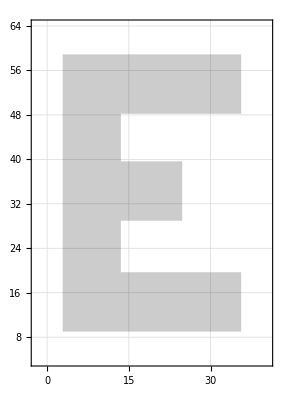
{Е,-Graphics-,{{2.85117,58.8955},{35.6396,58.8955},{35.6396,48.2036},{13.5431,48.2036},{13.5431,39.6501},{24.803,39.6501},{24.803,28.9582},{13.5431,28.9582},{13.5431,19.6919},{35.6396,19.6919},{35.6396,9.},{2.85117,9.}}}

```mathematica
{Letter,FigLetter,Vertices}=Apply[
{First@#1,Uncompress@Last@#1,{##2}}&,
Import["C:\\NG\\NG21P01Problem.xlsx",{"Sheets","БельскаяЕ"}]]
```

Изображение фигуры и вершин

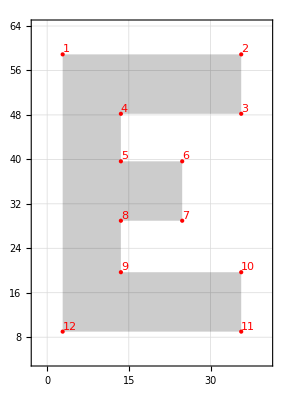

```mathematica
Show[FigLetter,Graphics[{Red, Thick,MapIndexed[{Point@#, Text[First@#2, #1, {-1,-1}]}&, Vertices]}, Hue[.33,1,1,.3]]]
```

```mathematica
Collect[(x-x1)/(x2-x1)-(y-y1)/(y2-y1),{x,y},Simplify]
```

x1/(x1-x2)+x/(-x1+x2)+y/(y1-y2)+y1/(-y1+y2)

```mathematica
Collect[%(x2-x1)(y2-y1),{x,y},Simplify]
```

(x1-x2) y+x2 y1-x1 y2+x (-y1+y2)

Построение функции, которая по двум точкам даёт коэффициенты общего уравнения прямой, проходящей через эти две точки

```mathematica
ClearAll[P2L];
P2L[{{x1_,y1_},{x2_,y2_}}]:=(-{y2-y1,-x2+x1,x2 y1-x1 y2})/(√((y2-y1)^2+(-x2+x1)^2))
```

Функция, строящая полуплоскости, краями которых являются прямыми, проходящие через заданные точки

```mathematica
ClearAll[draw];
draw[{{x1_,y1_},{x2_,y2_}}]:=Show[FigLetter, Graphics[{Opacity[0.4, Blue],HalfPlane[{{x1, y1}, {x2,y2}},P2L[{{x1, y1}, {x2,y2}}]⟦1;;2⟧]}],
Graphics[{Red, Thick,MapIndexed[{Point@#, Text[First@#2, #1, {-1,-1}]}&, Vertices]}]]
```

Список пар точек, через которые будут проходить прямые указанные выше

```mathematica
listVer={{2,1},{11,2},{4,3},{9,4},{6,5},{7,6},{8,7},{10,9},{12,11},{1,12}};
```

```mathematica
Export["C:\\NG\\~.xlsx",listVer]
```

C:\NG\~.xlsx

Построение всех полуплоскостей

```mathematica
Manipulate[draw@Vertices⟦listVer⟦v⟧⟧,{{v,1,"Полуплоскть"},Range[10]},ControlType->SetterBar]
```

## 2. Искусственный нейрон

```mathematica
ClearAll[kmANN];
kmANN[W_]:=Sign[W.Append[#, 1]]&
```

Синаптические весы первого слоя (коэффициенты общих уравнений прямых, полученных ранее)

```mathematica
WW1=P2L@Vertices⟦listVer⟦#⟧⟧&/@Range[10]
```

{{0.,-1.,58.8955},{-1.,0.,35.6396},{0.,1.,-48.2036},{-1.,0.,13.5431},{0.,-1.,39.6501},{-1.,0.,24.803},{0.,1.,-28.9582},{0.,-1.,19.6919},{0.,1.,-9.},{1.,0.,-2.85117}}

```mathematica
Export["C:\\NG\\~.xlsx",WW1]
```

C:\NG\~.xlsx

## 3. Однослойный персептрон

Функция kmANN дейтсвует на каждую точку. Получаем значения 1 или - 1 (левее или правее относительно прямой)

```mathematica
ClearAll[drawplanes];drawplanes[W_]:=Show[FigLetter, ContourPlot[kmANN[W]@{x,y},{x,-10,50},{y,0,70},Contours->{0},ContourShading->{Hue[0.00,1,1,0.3], Hue[0.67,1,1,0.3]}, GridLines->Automatic]]
```

```mathematica
Manipulate[drawplanes@P2L[Vertices⟦listVer⟦v⟧⟧],{{v,1,"Нейрон первого слоя"},Range[10]}, ControlType->SetterBar]
```

## 4. Выпуклый многоугольник

Синаптические весы второго слоя. 1, если многоугольник принадлежит полуплоскости, 0, если полуплоскость не участвует в создании многоугольника, -1, если полуплоскость участвует в создании многоугольника, но многоугольник ей не принадлежит(находится по другую сторону от края). Последние элементы каждого подсписка списка - подобранные весы-смещения.

```mathematica
WW2={{1,1,0,0,0,0,0,0,1,1,-3},{1,1,-1,-1,0,0,0,-1,1,1,-5.5},{1,1,0,-1,1,1,1,0,1,1,-7.5}}
```

{{1,1,0,0,0,0,0,0,1,1,-3},{1,1,-1,-1,0,0,0,-1,1,1,-5.5},{1,1,0,-1,1,1,1,0,1,1,-7.5}}

```mathematica
Export["C:\\NG\\~.xlsx",WW2]
```

C:\NG\~.xlsx

Вершины многоугольников

```mathematica
polyList={{1,2,11,12},{3,4,9,10},{5,6,7,8}};
```

```mathematica
polyL=Vertices⟦#⟧&/@polyList
```

{{{2.85117,58.8955},{35.6396,58.8955},{35.6396,9.},{2.85117,9.}},{{35.6396,48.2036},{13.5431,48.2036},{13.5431,19.6919},{35.6396,19.6919}},{{13.5431,39.6501},{24.803,39.6501},{24.803,28.9582},{13.5431,28.9582}}}

## 5. Двухслойный персептрон

Функция для изображения необходимых многоугольников. kmANN[WW1]@{x,y} получение вектора, состоящего из 1 и -1(всего таких элементов 10) для каждой точки. Каждый элемент вектора показывает расположение относительно прямых (краев полученных ранее полуплоскостей). kmANN[W]@(kmANN[WW1]@{x,y}) находим расположение (-1 или 1) для этой точки уже относительно заданного многоугольника.

```mathematica
ClearAll[drawpoly];drawpoly[W_]:=Show[FigLetter, ContourPlot[kmANN[W]@(kmANN[WW1]@{x,y}),{x,-10,50},{y,0,70},Contours->{0},ContourShading->{Hue[0.00,1,1,0.3], Hue[0.67,1,1,0.3]}, GridLines->Automatic]]
```

```mathematica
Manipulate[drawpoly@WW2⟦v⟧,{{v,1,"Нейрон второго слоя"},Range[3]}, ControlType->SetterBar]
```

## 6. Трехслойный персептрон

Синаптические весы третьего слоя. 1- первый многоугольник участвует в создании буквы, -1 - второй не участвует, 1 - третий участвует, 0.5-вес-смещение (иными словами, из большого прямоугольника удаляется средний и добавляется малый)

```mathematica
WW3={1,-1,1,0.5}
```

{1,-1,1,0.5}

Построение многоугольника, являющегося начертанием буква Е. Аналогично как и в случае с двухслойным персептроном.

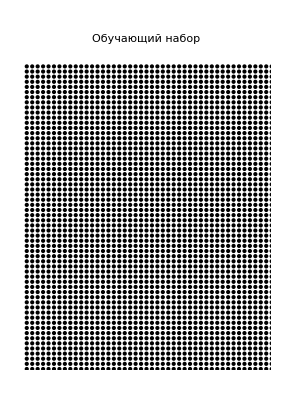

```mathematica
Graphics[{Point[#,If[kmANN[WW3]@(kmANN[WW2]@(kmANN[WW1]@#))>0,VertexColors->Blue, VertexColors->Red]]&/@Tuples[Range[-2,62],2]},PlotLabel->"Обучающий набор",PlotRange->{{-2,42},{4,64}}]
```

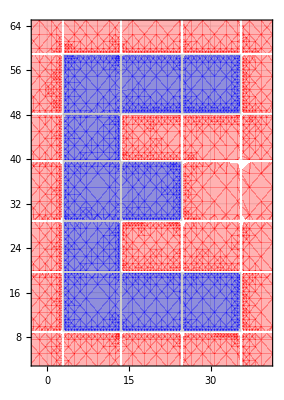

```mathematica
Show[FigLetter, ContourPlot[kmANN[WW3]@(kmANN[WW2]@(kmANN[WW1]@{x,y})),{x,-10,50},{y,0,70},Contours->{0},ContourShading->{Hue[0.00,1,1,0.3], Hue[0.67,1,1,0.3]}, GridLines->Automatic]]
```

```mathematica
Manipulate[Show[FigLetter,Graphics[{PointSize[0.05],Dynamic@Point[p, If[kmANN[WW3]@(kmANN[WW2]@(kmANN[WW1]@p))>0,VertexColors->Blue, VertexColors->Red]],Locator[Dynamic[p],None]}],PlotLabel->Style[p,If[kmANN[WW3]@(kmANN[WW2]@(kmANN[WW1]@p))>0,Blue, Red], Thick]],{{p,{20,35}},Locator,Appearance->None}]
```